```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
lptov1Color=ColorData["Legacy","Turquoise"];
```

```mathematica
lptopmColor=RGBColor["#009ade"];
```

```mathematica
dateMouseSessionListLPtoV1={{"081522","Mouse23054","Session1"},{"081622","Mouse23054","Session1"},{"043023","Mouse23134","Session2"},{"043023","Mouse23167","Session1"},{"050423","Mouse23167","Session1"}};
```

```mathematica
dateMouseSessionListLPtoPM={{"062222","Mouse22597","Session1"},{"062222","Mouse22597","Session2"},{"072122","Mouse23087","Session1"},{"072122","Mouse23096","Session1"},{"072122","Mouse23096","Session2"},{"073022","Mouse23087","Session1"},{"080122","Mouse23079","Session1"},{"080222","Mouse23079","Session1"},{"080122","Mouse23060","Session1"},{"080222","Mouse23060","Session1"}};
```

```mathematica
roisListLPtoV1=Table[Range[Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLPtoV1[[n,1]],"/",dateMouseSessionListLPtoV1[[n,2]],"/",dateMouseSessionListLPtoV1[[n,3]],"/dFOverF0TimeSeries_CellBodies/"]]]]],{n,1,Length[dateMouseSessionListLPtoV1]}];
```

```mathematica
roisListLPtoPM=Table[Range[Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLP[[n,1]],"/",dateMouseSessionListLP[[n,2]],"/",dateMouseSessionListLP[[n,3]],"/dFOverF0TimeSeries_CellBodies/"]]]]],{n,1,Length[dateMouseSessionListLP]}];
```

```mathematica
(**********************************************)
(*******Generate plot in Figure S6B****************) 
(**********************************************)
```

```mathematica
staFRLPtoV1=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLPtoV1[[n,1]],"/",dateMouseSessionListLPtoV1[[n,2]],"/",dateMouseSessionListLPtoV1[[n,3]],"/PMSpikeTriggeredAvgAxonActivity_FRestimates/","overallFRsta",ToString[roi],".txt"],"List"],{roi,roisListLPtoV1[[n]]}],{n,1,Length[dateMouseSessionListLPtoV1]}];
```

```mathematica
catenatedSTAfrLPtoV1=Flatten[staFRLPtoV1,1];
```

```mathematica
meanCatenatedSTAfrLPtoV1=Mean[catenatedSTAfrLPtoV1];
```

```mathematica
semCatenatedSTAfrLPtoV1=(#/Sqrt@Length[catenatedSTAfrLPtoV1])&/@StandardDeviation[catenatedSTAfrLPtoV1];
```

```mathematica
staFRLPtoPM=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLPtoPM[[n,1]],"/",dateMouseSessionListLPtoPM[[n,2]],"/",dateMouseSessionListLPtoPM[[n,3]],"/PMSpikeTriggeredAvgAxonActivity_FRestimates/","overallFRsta",ToString[roi],".txt"],"List"],{roi,roisListLPtoPM[[n]]}],{n,1,Length[dateMouseSessionListLPtoPM]}];
```

```mathematica
catenatedSTAfrLPtoPM=Flatten[staFRLPtoPM,1];
```

```mathematica
meanCatenatedSTAfrLPtoPM=Mean[catenatedSTAfrLPtoPM];
```

```mathematica
semCatenatedSTAfrLPtoPM=(#/Sqrt@Length[catenatedSTAfrLPtoPM])&/@StandardDeviation[catenatedSTAfrLPtoPM];
```

```mathematica
(************************************************)
```

```mathematica
(***********************)
```

```mathematica
staRandFRLPtoV1=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLPtoV1[[n,1]],"/",dateMouseSessionListLPtoV1[[n,2]],"/",dateMouseSessionListLPtoV1[[n,3]],"/PMSpikeTriggeredAvgAxonActivity_FRestimates/","overallFRstaRand",ToString[roi],".txt"],"List"],{roi,roisListLPtoV1[[n]]}],{n,1,Length[dateMouseSessionListLPtoV1]}];
```

```mathematica
catenatedSTARfrLPtoV1=Flatten[staRandFRLPtoV1,1];
```

```mathematica
meanCatenatedSTARfrLPtoV1=Mean[catenatedSTARfrLPtoV1];
```

```mathematica
semCatenatedSTARfrLPtoV1=(#/Sqrt@Length[catenatedSTARfrLPtoV1])&/@StandardDeviation[catenatedSTARfrLPtoV1];
```

```mathematica
staRandFRLPtoPM=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLPtoPM[[n,1]],"/",dateMouseSessionListLPtoPM[[n,2]],"/",dateMouseSessionListLPtoPM[[n,3]],"/PMSpikeTriggeredAvgAxonActivity_FRestimates/","overallFRstaRand",ToString[roi],".txt"],"List"],{roi,roisListLPtoPM[[n]]}],{n,1,Length[dateMouseSessionListLPtoPM]}];
```

```mathematica
catenatedSTARfrLPtoPM=Flatten[staRandFRLPtoPM,1];
```

```mathematica
meanCatenatedSTARfrLPtoPM=Mean[catenatedSTARfrLPtoPM];
```

```mathematica
semCatenatedSTARfrLPtoPM=(#/Sqrt@Length[catenatedSTARfrLPtoPM])&/@StandardDeviation[catenatedSTARfrLPtoPM];
```

```mathematica
(*****************************************************)
```

```mathematica
catenatedLPtoV1rawMinusShuff=catenatedSTAfrLPtoV1-catenatedSTARfrLPtoV1;
```

```mathematica
meanCatenatedLPtoV1rawMinusShuff=Mean[catenatedLPtoV1rawMinusShuff];
```

```mathematica
semCatenatedLPtoV1rawMinusShuff=(#/Sqrt@Length[catenatedLPtoV1rawMinusShuff])&/@StandardDeviation[catenatedLPtoV1rawMinusShuff];
```

```mathematica
(*************************)
```

```mathematica
catenatedLPtoPMrawMinusShuff=catenatedSTAfrLPtoPM-catenatedSTARfrLPtoPM;
```

```mathematica
meanCatenatedLPtoPMrawMinusShuff=Mean[catenatedLPtoPMrawMinusShuff];
```

```mathematica
semCatenatedLPtoPMrawMinusShuff=(#/Sqrt@Length[catenatedLPtoPMrawMinusShuff])&/@StandardDeviation[catenatedLPtoPMrawMinusShuff];
```

```mathematica
lptov1STArms=ListLinePlot[{meanCatenatedLPtoV1rawMinusShuff,meanCatenatedLPtoV1rawMinusShuff+semCatenatedLPtoV1rawMinusShuff,meanCatenatedLPtoV1rawMinusShuff-semCatenatedLPtoV1rawMinusShuff},Filling->{1->{{2},Directive[Opacity[0.2],lptov1Color]},1->{{3},Directive[Opacity[0.2],lptov1Color]},4->{{5},Directive[Opacity[0.2],lptov1Color]},4->{{6},Directive[Opacity[0.2],lptov1Color]}},PlotStyle->{{lptov1Color,Thickness[0.006]},Transparent,Transparent},DataRange->{-4,4},PlotRange->{{-4,4},{-0.0005,0.003}},FrameTicks->{{LinTicks[-0.0005,0.003,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-4,4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lptopmSTArms=ListLinePlot[{meanCatenatedLPtoPMrawMinusShuff,meanCatenatedLPtoPMrawMinusShuff+semCatenatedLPtoPMrawMinusShuff,meanCatenatedLPtoPMrawMinusShuff-semCatenatedLPtoPMrawMinusShuff},Filling->{1->{{2},Directive[Opacity[0.2],lptopmColor]},1->{{3},Directive[Opacity[0.2],lptopmColor]},4->{{5},Directive[Opacity[0.2],lptopmColor]},4->{{6},Directive[Opacity[0.2],lptopmColor]}},PlotStyle->{{lptopmColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-4,4},PlotRange->{{-4,4},{-0.0005,0.003}},FrameTicks->{{LinTicks[-0.0005,0.003,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-4,4,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

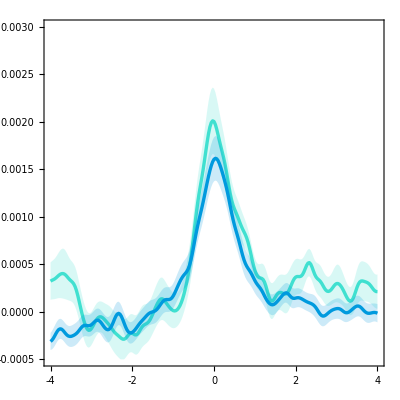

```mathematica
Show[lptov1STArms,lpSTArms]
```

```mathematica
(**********************************************)
(*******Generate plot in Figure S6C****************) 
(**********************************************)
```

```mathematica
lptov1PeakSizes=Table[Table[Max[staFRLPtoV1[[n,m]]]-Mean[Table[staFRLPtoV1[[n,m,i]],{i,1,60}]],{m,1,Length[roisListLPtoV1[[n]]]}],{n,1,Length[roisListLPtoV1]}];
```

```mathematica
lpPeakSizes=Table[Table[Max[staFRLP[[n,m]]]-Mean[Table[staFRLP[[n,m,i]],{i,1,60}]],{m,1,Length[roisListLP[[n]]]}],{n,1,Length[roisListLP]}];
```

```mathematica
(******)
```

```mathematica
(**********************)
```

```mathematica
lptov1AxonCharts=Show[BoxWhiskerChart[Flatten@lptov1PeakSizes,{{"Whiskers", Directive[Darker@lptov1Color,Thick]}, {"Fences", Directive[Darker@lptov1Color,Thick]},{"MedianMarker", Directive[Darker@lptov1Color,Thickness[0.009]]}},PlotRange->{All,{0,0.011}},ChartStyle->Directive[lptov1Color,Opacity[0.3]],Frame->False],DistributionChart[Flatten@lptov1PeakSizes,PlotRange->{All,{0,0.011}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lptov1Color],Frame->False],FrameTicks->{{LinTicks[0,0.011,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lptopmAxonCharts=Show[BoxWhiskerChart[Flatten@lptopmPeakSizes,{{"Whiskers", Directive[Darker@lptopmColor,Thick]}, {"Fences", Directive[Darker@lptopmColor,Thick]},{"MedianMarker", Directive[Darker@lptopmColor,Thickness[0.009]]}},PlotRange->{All,{0,0.011}},ChartStyle->Directive[lptopmColor,Opacity[0.3]],Frame->False],DistributionChart[Flatten@lptopmPeakSizes,PlotRange->{All,{0,0.011}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lptopmColor],Frame->False],FrameTicks->{{LinTicks[0,0.011,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[Flatten@lptopmPeakSizes,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{0,0.011}},ChartStyle->Transparent,Frame->False],DistributionChart[Flatten@lptopmPeakSizes,PlotRange->{All,{0,0.011}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[0,0.011,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

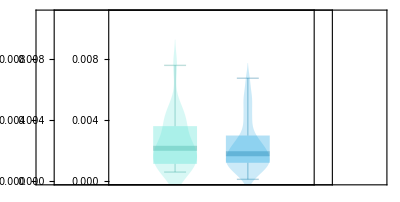

```mathematica
GraphicsRow[{lptov1AxonCharts,lptopmAxonCharts,transp},Spacings->{{-280,-280,-420}}]
```